```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/blogit" ]
```

/Users/pjoot/project/figures/blogit

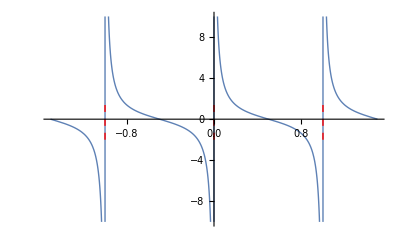

{sumUsingContourFig1.eps,sumUsingContourFig1pn.png}

```mathematica
sumUsingContourFig1 = Plot[Cot[Pi x], {x,-1.5,1.5}, PlotStyle->Thick, Exclusions->None,(*Ensure the function is plotted across poles*)Epilog->{Dashed,Red,(*Style for the asymptotes*)Table[Line[{{n,-2},{n,2}}],{n,-1,1}]},PlotRange->{{-1.5,1.5},{-10, 10}},AxesOrigin->{0,0},AxesStyle->Thick]

peeters`exportForLatex["sumUsingContourFig1", sumUsingContourFig1]
```

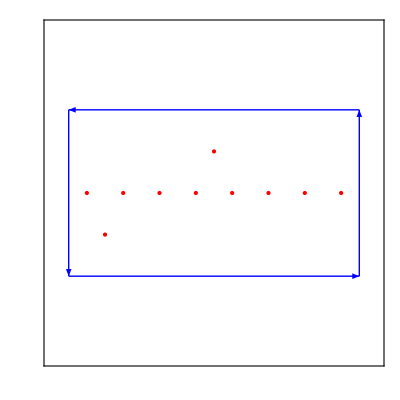

{sumUsingContourFig2.eps,sumUsingContourFig2pn.png}

```mathematica
ClearAll[a,b,poles1, poles2, poles, sumUsingContourFig2]
a=-3;
b=4;

poles1=Table[{n,0},{n,a,b}];
poles2 = {{1/2,1/2},{-5/2,-1/2}};
poles = Flatten[{poles1, poles2}, 1];


rectangularContour={Arrowheads[0.03],Arrow[{{a-0.5,-1},{b+0.5,-1}}],Arrow[{{b+0.5,-1},{b+0.5,1}}],Arrow[{{b+0.5,1},{a-0.5,1}}],Arrow[{{a-0.5,1},{a-0.5,-1}}]};

sumUsingContourFig2 = Graphics[{
Blue,
Thick,
rectangularContour,
Red,
PointSize[Large],
Point[poles]
},
AxesOrigin->{0,0},
PlotRange->{{a-1,b+1},{-2,2}},
AspectRatio->1,
Axes->True,
Frame->True,
FrameTicks->None
]

peeters`exportForLatex["sumUsingContourFig2", sumUsingContourFig2]
```